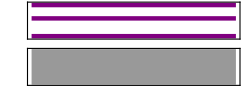

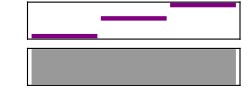

-Graphics-

```mathematica
Sound[SoundNote[{0,4,7}]]
Sound[SoundNote[#]&/@{0,4,7}]
Sound[SoundNote/@{0,4,7}]
```

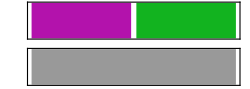

```mathematica
Sound[{SoundNote["G",1,"Violin"],SoundNote["G",1,55]}]
```

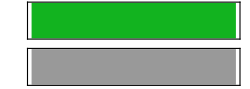

```mathematica
Sound[SoundNote["G",1,55]]
```

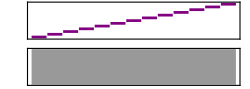

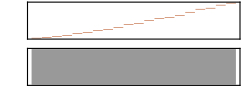

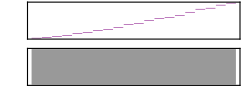

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
Sound[Table[SoundNote[Prime[i]-20,0.1,"Woodblock"],{i,20}]]
Sound[Table[SoundNote[Prime[i]-20,0.1,"Piano"],{i,20}]]
```

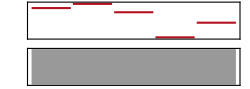

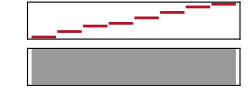

```mathematica
Sound[SoundNote[#,0.5, "Polysynth"]&/@{2,4,0,-12,-5}]
Sound[SoundNote[#,0.5, "Polysynth"]&/@{0,2,4,5,7,9,11,12}]
```

```mathematica
EmitSound[%23]
```

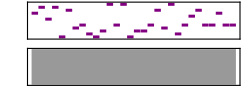

```mathematica
Sound[SoundNote/@RandomInteger[12,30],4]
```

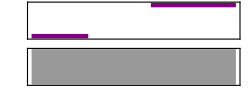

```mathematica
Sound[{SoundNote["C",0.2],SoundNote[None,0.2],SoundNote["G",0.3]}]
```

两种乐器演奏的具有重叠的音符：

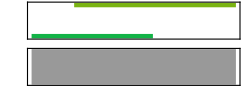

```mathematica
Sound[{SoundNote["C",{0,0.3},"Tuba"],SoundNote["G",{0.1,0.5},"Cello"]}]
```

给出多个音符的风格：

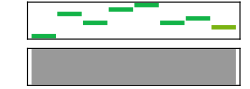

```mathematica
Sound[{"Tuba",SoundNote/@{0,5,3,6,7,3,4},"Cello",SoundNote[2]}]
```

指定一个没有音高的打击乐：

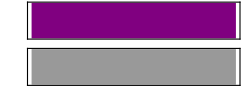

```mathematica
Sound[SoundNote["Snare"]]
```

演奏一个小提琴的升降序列，每个音符 0.1 秒：

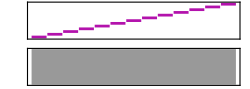

```mathematica
Sound[Table[SoundNote[i,0.1,"Violin"],{i,0,12}]]
```

```mathematica
Sound[SoundNote[#,0.5, "Polysynth"]&/@{2,4,0,-12,-5}]
```

-Graphics-

用随机乐器生成随机旋律：

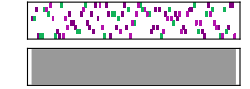

```mathematica
Sound[Table[SoundNote[RandomInteger[7],.2,RandomChoice[{"Piano","Guitar","Violin"}]],100]]
```

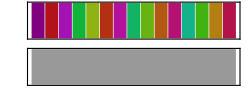

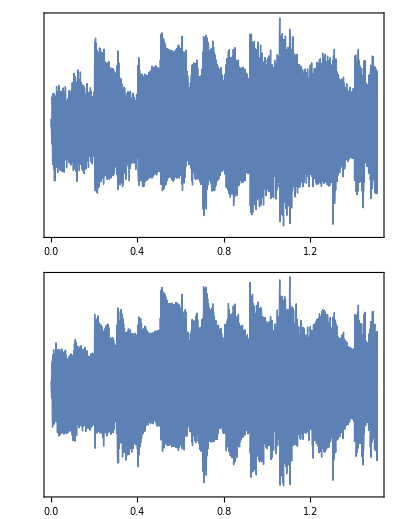

vvv.ogg

vvv.mid

```mathematica
Sound[Table[SoundNote[0,0.1,i],{i,15}]]
Audio@Sound[Table[SoundNote[0,0.1,i],{i,15}]]
AudioPlot[%]
Export["vvv.ogg",Sound[Table[SoundNote[0,0.1,i],{i,15}]]]
Export["vvv.mid",Sound[Table[SoundNote[0,0.1,i],{i,15}]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["vvv.mid"]]]
```

```mathematica
SystemOpen["vvv.ogg"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["vvv.mp3"]]]
```

```mathematica
SystemOpen["vvv.mp3"]
```

```mathematica
Expand[(α+β)^3]
```

α^3+3 α^2 β+3 α β^2+β^3

```mathematica
Factor[α^3+3 α^2 β+3 α β^2+β^3]
```

(α+β)^3

```mathematica
N[Pi,50]
```

3.1415926535897932384626433832795028841971693993751

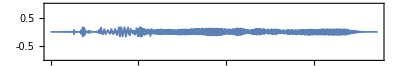

```mathematica
0.5Audio[File["ExampleData/car.mp3"]]
Audio[File["vvv.mp3"]]
.2Audio["ExampleData/car.mp3"]//AudioPlot
```

```mathematica
Export["perc.mid",Sound[ SoundNote["RideCymbal", #] & /@ {0.26,0.1,0.26,0.1,2} ] ]
```

perc.mid

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["perc.mid"]]]
```